# CS164 3.2 PCW

## Sublevel Sets and Coercive

Pre-Class Work

(1) For each of the functions below, plot a diagram of their level sets and determine whether or not the functions are coercive. You may use a graphical package to plot
the level sets.

The function f(x, y) = x + y  
is not coercive since the output is constant as the input ||X|| tends towards infinity. As a general rule, all linear functions are not coercive since they can be written in the form:
f(x, y) = ax + by + c
As ||X|| goes to infinity, the output of the function f(x, y) converges towards c. Thus f(x, y) is not coercive.

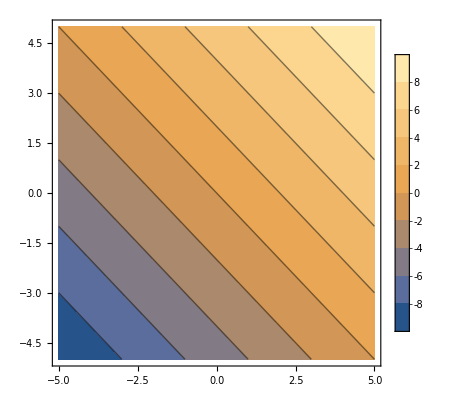

```mathematica
ContourPlot[x+y,{x,-5,5},{y,-5,5}, PlotLegends->Automatic]
```

The function f(x, y) = x^2 + 4*y^2
The function is coercive since when the norm ||X|| = Sqrt(x^2 + y^2)
tends towards infinity, the output of the function f goes to infinity.

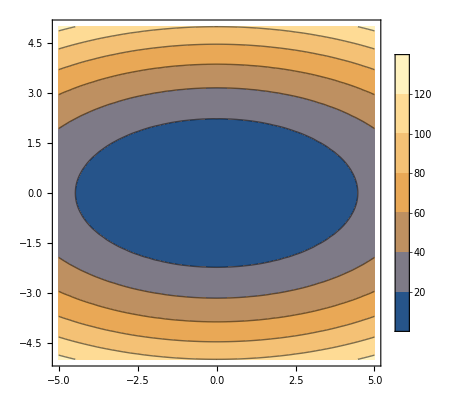

```mathematica
ContourPlot[x^2+4*y^2,{x,-5,5},{y,-5,5}, PlotLegends->Automatic]
```

The function f(x, y) = x * y
The function is not coercive since it goes to infinity on some path on which the norm tends to infinity.

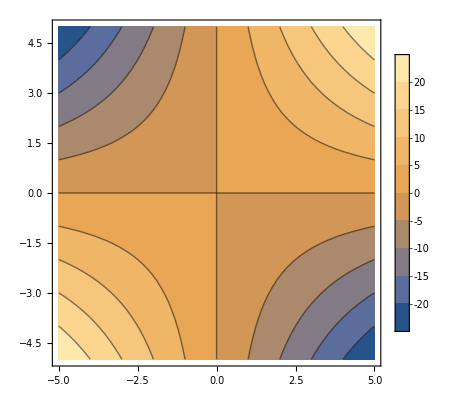

```mathematica
ContourPlot[x*y,{x,-5,5},{y,-5,5}, PlotLegends->Automatic]
```

The function f(x , y) = x^2 - y^2 is not coercive
Since the function is equal to 0 when x = y then the output of the function is constant along the line x = y

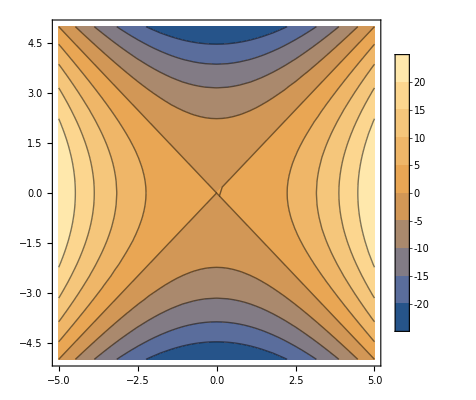

```mathematica
ContourPlot[x^2-y^2,{x,-5,5},{y,-5,5}, PlotLegends->Automatic]
```

The function f(x, y) = x^2+2*x*y+y^2 = (x + y)^2
Coercive, as the norm tends to infinity, the output of the function also goes to infinity

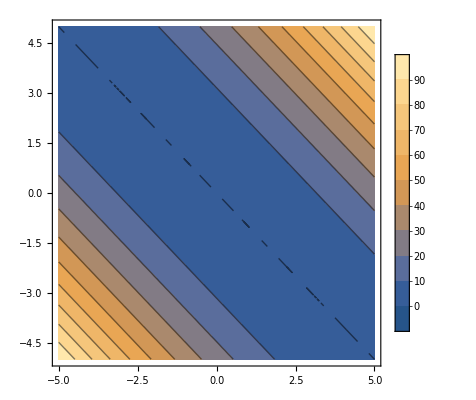

```mathematica
ContourPlot[x^2+2*x*y+y^2,{x,-5,5},{y,-5,5}, PlotLegends->Automatic]
```

The function f(x, y) = x^4+2*x*y+y^4
The function is coercive since it converges towards infinity on all path where the norm goes to infinity.

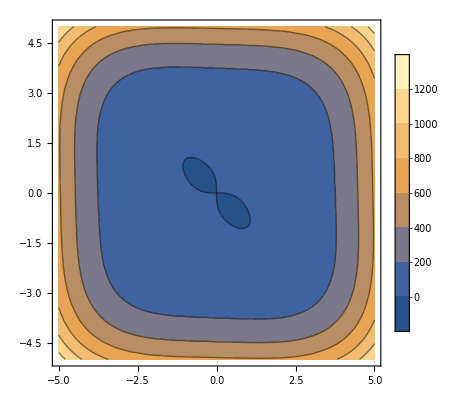

```mathematica
ContourPlot[x^4+2*x*y+y^4,{x,-5,5},{y,-5,5}, PlotLegends->Automatic]
```

(2) Prove that the following function is coercive and describe its sublevel sets mathematically (no need to plot them).

The norm of this function is written as:
||X|| = Sqrt(x^2 + y^2 + z^2)
We can transform the function to be:
f(||X||) = Exp( ||X||^2 )
As the norm ||X|| goes to infinity, the function f(||X||) tends to infinity.

The sublevel sets are in the form of spheres as shown in the plot below.

```mathematica
ContourPlot3D[Exp[x^2+y^2+z^2],{x,-1/4,1/4},{y,-1/4,1/4},{z,-1/4,1/4},PlotLegends->Automatic]
```

-Graphics3D-